```mathematica
s[t_]:=t^3-9/2 t^2-7t
s'[t]
s''[t]
Solve[s''[t]==0,t]
```

-7-9 t+3 t^2

-9+6 t

{{t→3/2}}

```mathematica
h[t_]:=10t-0.83 t^2;
Solve[h[t]==25,t]
h'[3.540297815892975]
```

{{t→3.5403},{t→8.50789}}

4.12311

```mathematica
h[t_]:=80t-16 t^2
h'[t]
Solve[h'[t]==0,t]//N
h[2.5]
```

80-32 t

{{t→2.5}}

100.

```mathematica
a[r_]:=π r^2
diff[r1_,r2_]:=(a[r2]-a[r1])/(r2-r1)//N
diff[2,2.1]
```

12.8805

```mathematica
Head[Pi//N]
```

Real

```mathematica
s[r_]:=4 π r^2;
s'[3]//N
```

75.3982

```mathematica
V[t_]:=5000(1-t/40)^2
V'[t]
V'[{5,10,20,40}]//N
```

250 (-1+t/40)

{-218.75,-187.5,-125.,0.}

```mathematica
250 (-1+t/40)//Simplify//N//Expand
```

-250.+6.25 t

```mathematica
F[r_]:=(G M m)/r^2
F'[r]
```

-(2 G m M)/r^3

```mathematica
Solve[-2==(-2k)/20000^3,k]
```

{{k→8000000000000}}

```mathematica
G'[r_]:=(-2 8 10^12)/r^3
G'[10000]
```

-16

```mathematica
n[t_]:=400 3^t
n'[t]
n'[2.5]
```

400 3^t Log[3]

6850.27

```mathematica
f[t_]:=140/(1+6 Exp[-0.7t])
f[t]
```

140/(1+6 ⅇ^(-0.7 t))

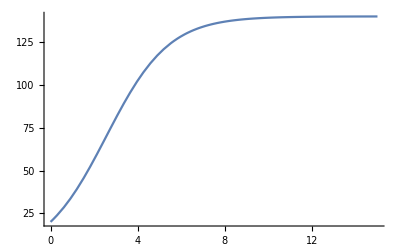

```mathematica
Plot[140/(1+6 ⅇ^(-0.7 t)),{t,0,15}]
```

```mathematica
Solve[{20==a/(1+b),12==(0.7a b)/(1+b)^2},{a,b}]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{a→140.,b→6.}}

```mathematica
f[length_,tension_,density_]:=1/(2length)Sqrt[tension/density]
D[f[L,T,D],{T}]
```

1/(4 D L √(T/D))

```mathematica
cost[x_]:=1200+12x-0.1 x^2+0.0005 x^3
cost'[x]//TraditionalForm
cost'[200]
cost[201]-cost[200]
```

0.0015 x^2-0.2 x+12

32.

32.2005

```mathematica
f[n_]:=(k n)/(1+n^2)
Dt[f[n],n,Constants->k]//Simplify
```

-(k (-1+n^2))/((1+n^2)^2)

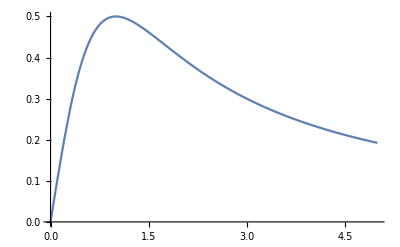

```mathematica
Plot[f[x],{x,0,5}]
```

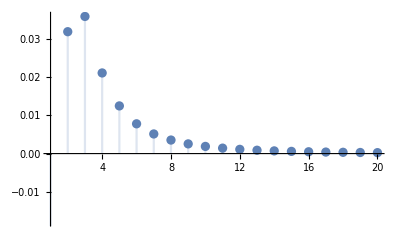

```mathematica
DiscretePlot[(2 (-3 n+n^3))/((1+n^2)^3),{n,1,20}]
```

```mathematica
Solve[-3n+n^3==0,n]
```

{{n→0},{n→-√3},{n→√3}}

```mathematica
Solve[0.75-3x==0,x]//N//Simplify
```

{{x→0.25}}

```mathematica
.75-1.5 .25
```

0.375

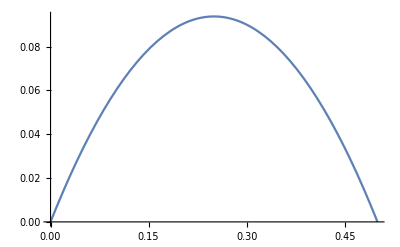

{0.09375,{x→0.25}}

```mathematica
Plot[0.75x-1.5 x^2,{x,0,0.5}]
Maximize[0.75x-1.5 x^2,x]
```

```mathematica
Solve[3x+2y==1.5,y]//Simplify
```

{{y→0.75-1.5 x}}

```mathematica
Clear[x,y]
```

```mathematica
Solve[0.75-1.5x==0,x]
```

{{x→0.5}}

```mathematica
0.25 10^6
```

250000.

```mathematica
Solve[3-3/x^2==0,x]
```

{{x→-1},{x→1}}

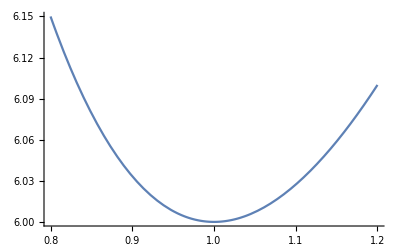

```mathematica
Plot[3x+3 x^-1,{x,0.8,1.2}]
```

```mathematica
area[x_]:=x (4 r^2-x^2)^(1/2)
Dt[area[x],x,Constants->r]//Simplify
```

-(2 (-2 r^2+x^2))/(√(4 r^2-x^2))

```mathematica
Solve[4 r^2-2 x^2==0,x]
```

{{x→-√2 r},{x→√2 r}}

```mathematica
Dt[A,f[x],Constants->{r}]
```

General::ivar: k\ x/1 + x^2 is not a valid variable.

Dt[A,(k x)/(1+x^2),Constants→{r}]

```mathematica
Solve[27==1/3 π r^2 h,h];
1/3 π r^2 h/.{r->2.6319242329642165,h->3.722114918056091}//N
```

27.0001

```mathematica
2 π r h /.%4
```

{162/r}

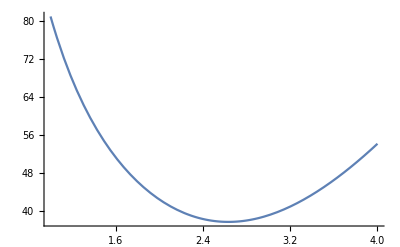

(-2088.43+6.28319 r^6)/(r^4 √((664.768+r^6)/r^4))

{37.6927,{r→2.63192}}

```mathematica
area[r_]:=π r Sqrt[r^2+81^2/π^2 r^-4]
Plot[area[x],{x,1,4}]
Dt[area[r],r]//N//Simplify
Minimize[{area[r],r>0},r]//N
```

```mathematica
Solve[%7==0,r]
```

{{r→-2.63192},{r→-1.31596-2.27931 ⅈ},{r→-1.31596+2.27931 ⅈ},{r→1.31596-2.27931 ⅈ},{r→1.31596+2.27931 ⅈ},{r→2.63192}}

```mathematica
(-2088.4311632518506+6.283185307179586 r^6)/(r^4 √((664.7682858773782+r^6)/r^4))
```

(-2088.43+6.28319 r^6)/(r^4 √((664.768+r^6)/r^4))

```mathematica
81^2/π^2//N
```

664.768

```mathematica
81/(π 2.63192^2)//N
```

3.72211